```mathematica
SetOptions[ListPlot,{AspectRatio->0.4,PlotStyle->{Red,Green,Blue,Black},Frame->True,FrameStyle->Thick,Axes->False,BaseStyle->{FontFamily->"Times",FontSize->18},ImageSize->500,GridLines->None,Joined->True,PlotRange->All,FrameLabel->{"x","y"}}];
```

```mathematica
dir1="2018-12-18-17-09-34";
SetDirectory["\\\\fed.cclrc.ac.uk\\org\\NLab\\ASTeC\\Projects\\VELA\\Work\\2018\\12\\20\\probe"];
fn=Select[FileNames[],StringTake[#,{-3,-1}]=="wxf"&]
data=Import[fn⟦2⟧];
Keys[data]
```

{outside_probe_log1.wxf,outside_probe_log2.wxf}

```mathematica
traceKeyHeads={"value_HRRG_CAVITY_FORWARD_PHASE","value_HRRG_CAVITY_FORWARD_POWER","value_HRRG_CAVITY_PROBE_PHASE","value_HRRG_CAVITY_PROBE_POWER","value_HRRG_CAVITY_REVERSE_PHASE","value_HRRG_CAVITY_REVERSE_POWER"}
tracesuffix={"_-2","_-1","_0","_1","_1"}
```

{value_HRRG_CAVITY_FORWARD_PHASE,value_HRRG_CAVITY_FORWARD_POWER,value_HRRG_CAVITY_PROBE_PHASE,value_HRRG_CAVITY_PROBE_POWER,value_HRRG_CAVITY_REVERSE_PHASE,value_HRRG_CAVITY_REVERSE_POWER}

{_-2,_-1,_0,_1,_1}

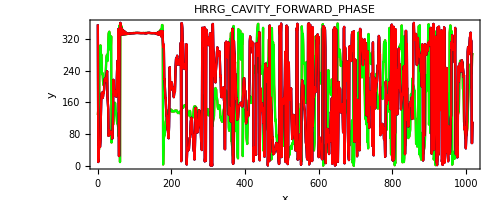
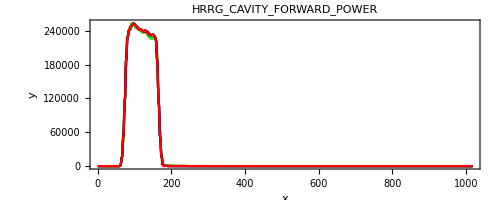
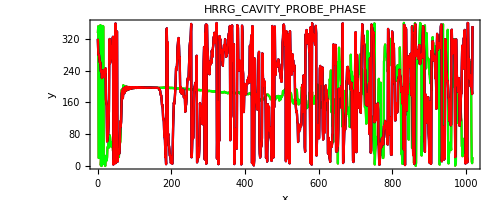
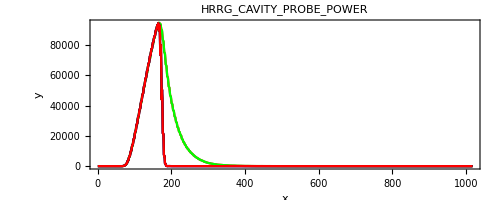
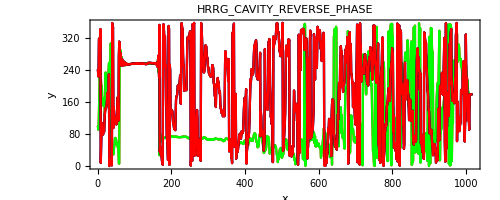
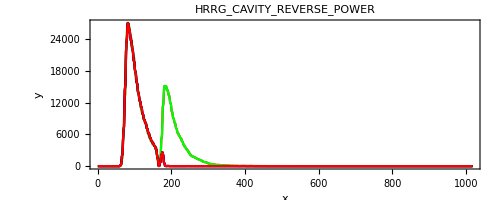

```mathematica
Table[
ListPlot[Lookup[data,traceKeyHeads⟦i⟧<>#&/@tracesuffix]⟦1⟧,PlotLabel->StringTake[traceKeyHeads⟦i⟧,{7,-1}]]
,{i,1,Length@traceKeyHeads}]
```

```mathematica
dir1="2018-12-18-17-09-34";
SetDirectory["D:\\VELA\\GIT Projects\\Software\Apps\\RF_Conditioner\\logs\\HRRG\\2018-12-18-17-09-34"];
fn=Select[FileNames[],StringTake[#,{-3,-1}]=="wxf"&]
data=Import[fn⟦2⟧];
```

{outside_probe_log1.wxf,outside_probe_log2.wxf}

```mathematica
getTraceData[fn_]:=Block[{data},
data=Import[fn];
Table[Lookup[data,traceKeyHeads⟦i⟧<>#&/@tracesuffix]⟦1⟧,{i,1,Length@traceKeyHeads}]
]
```

```mathematica
dtoplot=getTraceData["\\\\fed.cclrc.ac.uk\\org\\NLab\\ASTeC\\Projects\\VELA\\Work\\2018\\12\\20\\probe\\outside_probe_log2.wxf"];
Table[ListPlot[dtoplot⟦i⟧],{i,1,Length@traceKeyHeads}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

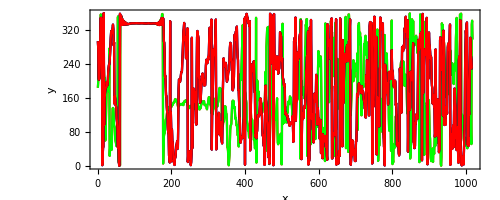
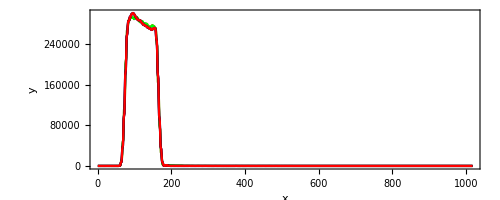
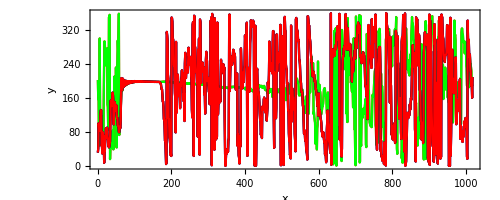
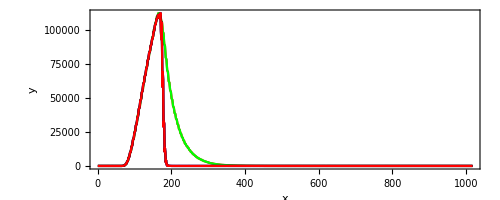
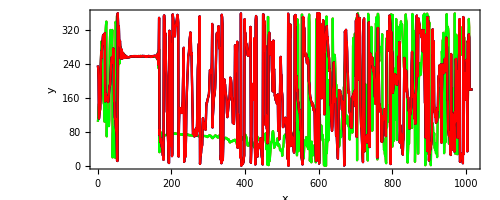
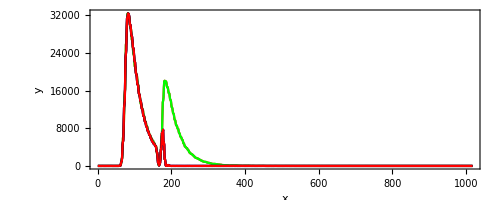

```mathematica
dtoplot=Table[Lookup[Import["\\\\fed.cclrc.ac.uk\\org\\NLab\\ASTeC\\Projects\\VELA\\Work\\2018\\12\\20\\outside_probe_log1.wxf"],traceKeyHeads⟦i⟧<>#&/@tracesuffix]⟦1⟧,{i,1,Length@traceKeyHeads}];
Table[ListPlot[dtoplot⟦i⟧],{i,1,Length@traceKeyHeads}]
```

```mathematica
Keys[Import["\\\\fed.cclrc.ac.uk\\org\\NLab\\ASTeC\\Projects\\VELA\\Work\\2018\\12\\20\\2018-12-20-15-31-37\\outside_probe_log1.wxf"]]
```

{{lo_mask_HRRG_CAVITY_PROBE_PHASE,num_collected_traces,DC,num_events,lo_mask_HRRG_CAVITY_FORWARD_PHASE,lo_mask_HRRG_CAVITY_REVERSE_POWER,lo_mask_KLYSTRON_REVERSE_PHASE,message,outside_mask_index,hi_mask_HRRG_CAVITY_FORWARD_PHASE,lo_mask_KLYSTRON_FORWARD_POWER,hi_mask_KLYSTRON_REVERSE_PHASE,mask_floor,trace_name,SOL,hi_mask_HRRG_CAVITY_REVERSE_PHASE,lo_mask_KLYSTRON_FORWARD_PHASE,hi_mask_HRRG_CAVITY_PROBE_PHASE,time_vector,lo_mask_HRRG_CAVITY_REVERSE_PHASE,is_collecting,vacuum,lo_mask_HRRG_CAVITY_PROBE_POWER,hi_mask_HRRG_CAVITY_PROBE_POWER,hi_mask_HRRG_CAVITY_REVERSE_POWER,hi_mask_KLYSTRON_FORWARD_POWER,lo_mask_KLYSTRON_REVERSE_POWER,hi_mask_KLYSTRON_REVERSE_POWER,lo_mask_HRRG_CAVITY_FORWARD_POWER,hi_mask_KLYSTRON_FORWARD_PHASE,hi_mask_HRRG_CAVITY_FORWARD_POWER}}

```mathematica
dtoplot=Table[Lookup[Import["\\\\fed.cclrc.ac.uk\\org\\NLab\\ASTeC\\Projects\\VELA\\Work\\2018\\12\\20\\2018-12-20-17-26-57\\outside_forward_log1.wxf"],traceKeyHeads⟦i⟧<>#&/@tracesuffix]⟦1⟧,{i,1,Length@traceKeyHeads}];
Table[ListPlot[dtoplot⟦i⟧],{i,1,Length@traceKeyHeads}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}